```mathematica
Lecture 14: Graph Theory
```

Key functions include

```mathematica
{Graph,UndirectedEdge,VertexList,VertexCount,EdgeList,EdgeCount,VertexLabels,GraphLayout,IsomorphicGraphQ,GraphData,AdjacencyMatrix,KirchhoffMatrix}
```

## Graph creation

### Exercise Subsection

A graph is a finite set of vertices V together with a set of edges (which are pairs of the form {v,w} where v, w are vertices).  Graphs can be created using Graph together with UndirectedEdge.  For example,

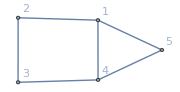

```mathematica
Graph[UndirectedEdge@@@{{1,2},{2,3},{3,4},{1,5},{1,4},{4,5}},VertexLabels->Automatic,ImageSize->Small]
```

The layout of this graph can be changed using the GraphLayout option in Graph, like this:

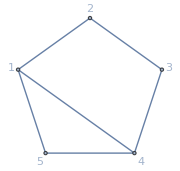

```mathematica
Graph[UndirectedEdge@@@{{1,2},{2,3},{3,4},{1,5},{1,4},{4,5}},VertexLabels->Automatic,GraphLayout->"CircularEmbedding",ImageSize->Small]
```

Create the Graph with vertices the integers 1,...,10 such that {i,j} is edge if and only if i<j and GCD[i,j] is 1.  Do this by selecting the appropriate pairs using Cases on Subsets[Range@10,{2}].  Select two different options for GraphLayout when visualizing the graph.

### Exercise Subsection

Create the Graph with vertices the all lists of 0’s and 1’s of length 4 with an edge between two lists if they differ in exactly one position.  Do this by selecting the appropriate pairs using Cases on Subsets[Tuples[{0,1},4],{2}].

### Exercise Subsection

Create the Graph with vertices all Permutations of 1,2,3,4 with an edge between two permutations a and b if PermutationMatrix@a==MatrixPower[PermutationMatrix@b,2].

### Exercise Subsection

Create the Graph with vertices all subsets of {1,2,3,4,5,6} with exactly 2 elements with an edge between two subsets if they are disjoint.

## Graph properties

### Exercise Subsection

The function IsomorphicGraphQ[G,H] tests to see if graphs G and H are isomorphic; that is, if they are the same graph after a relabeling or a redrawing of the vertices and edges.  Use IsomorphicGraph to verify that all the graphs in the next list L are isomorphic to one another.

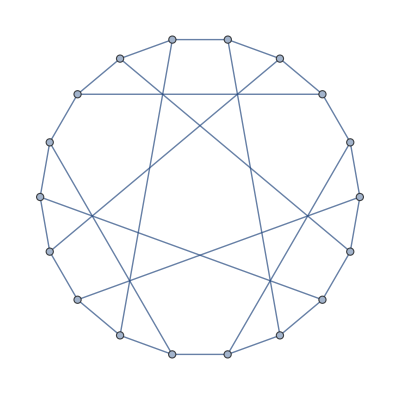
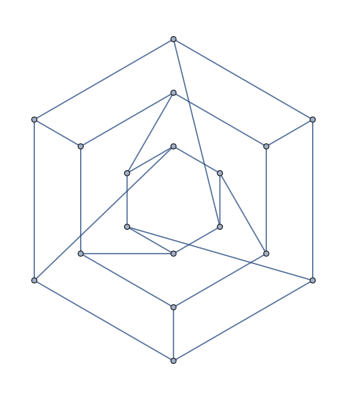
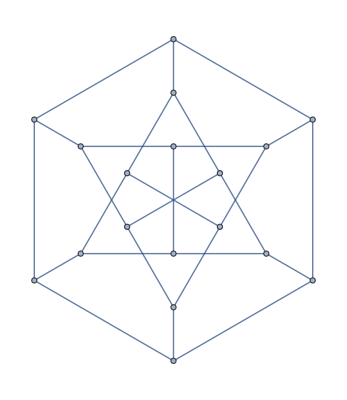
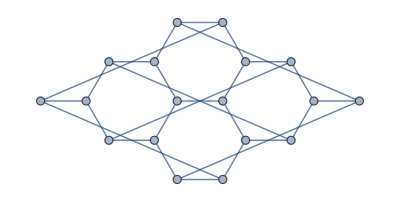
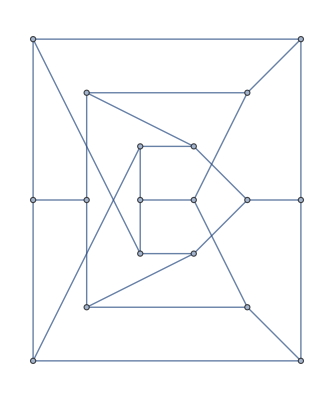
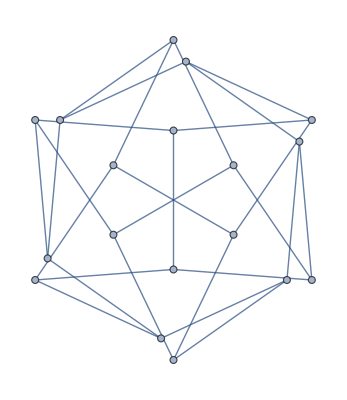
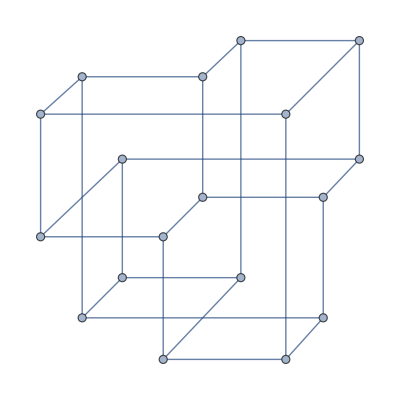
```mathematica
L={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

### Exercise Subsection

The function ConnectedGraphQ[G] tests to see if the graph G is connected, meaning there is a path between every pair of vertices (if the graph is in one piece).  The function RandomGraph[{m,n}] will produce a random graph with m vertices and n edges.  Use the Monte-Carlo method to estimate the probability that a random graph with 100 vertices and 200 edges is connected?  Experiment to find a value of n such that there is close to a 50% chance that a random graph with 100 vertices and n edges will be connected.

### Exercise Subsection

The function FindVertexColoring[G] finds the optimal way to assign colors (positive integers) to the vertices of G such that adjacent vertices are different colors.  An example of its use is in the next cell.

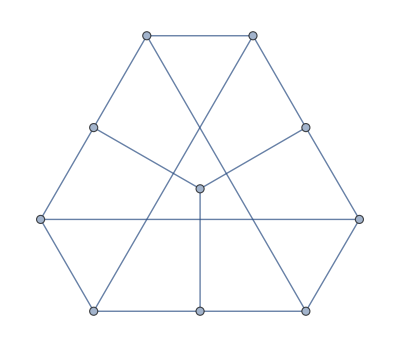
```mathematica
G=-Graphics-;
colors=FindVertexColoring[G,ColorData[110,"ColorList"]];
Graph[G,{VertexStyle->Thread[VertexList[G]->colors]},VertexSize->Medium,ImageSize->Small]
```

a. Color the following graph (which is the graph of the caffeine molecule) in the same way	as the above example.

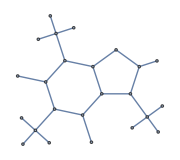
```mathematica
caffeine=-Graphics-;
```

b. The function VertexChromaticNumber[G] gives the minimum number of colors in such a coloring.  Estimate the average value (the average of a list can be found with Mean)  of VertexChromaticNumber for graphs with 25 vertices and 50 edges using RandomGraph.

### Exercise Subsection

The function FindPath[G,v,w,∞,All] finds all paths from vertex v to vertex w in G.  

a. Let m be the length of the longest path between any two vertices for the following graph:

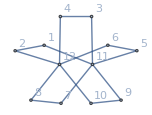
```mathematica
G=-Graphics-;
```

b. Find all paths of length m in G and then show that any three such longest paths must share at least one vertex.

c. It is an open problem to show that any three longest paths in any graph share a vertex.  The previous parts of this exercise verified the conjecture for the graph above.  Verify this conjecture for the following graph as well:

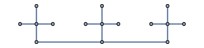
```mathematica
G=-Graphics-;
```

### Exercise Subsection

The function FindHamiltonianPath[G] finds a shortest path in G that visits every vertex once.  Use HighlightGraph to illustrate a Hamiltonian path in each of the graphs in the following list:

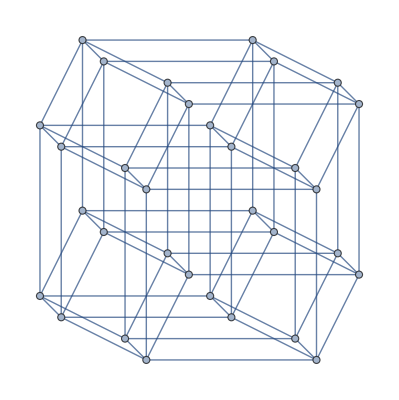
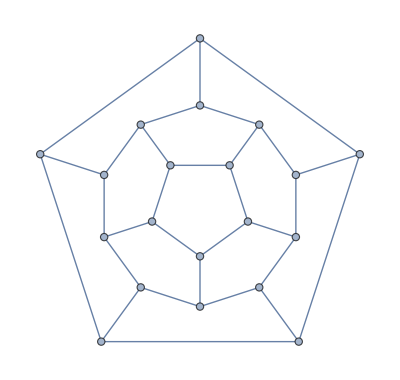
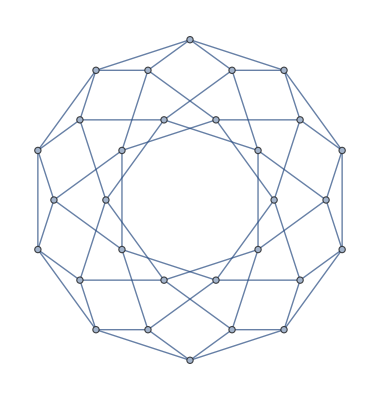
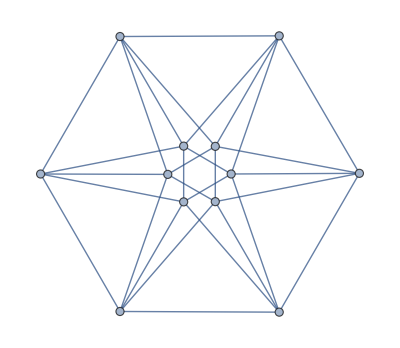
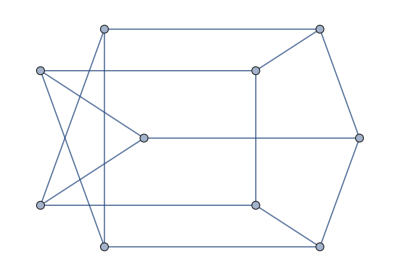
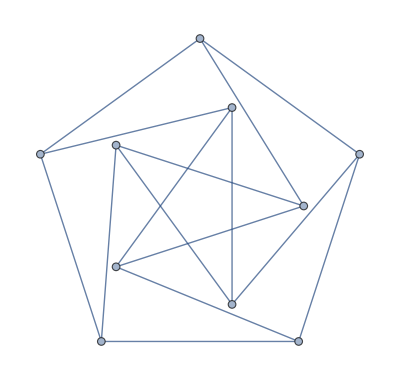
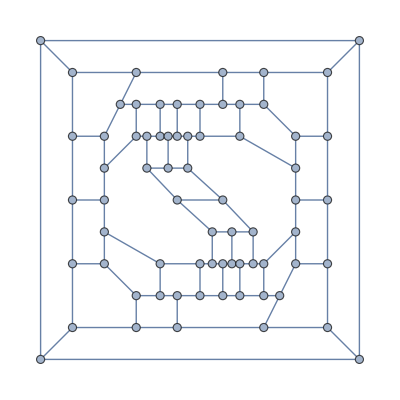
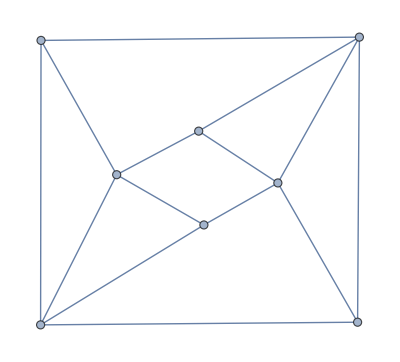
```mathematica
L={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
HighlightGraph[#,FindHamiltonianCycle@#]&/@L
```

### Exercise Subsection

a. The function HamiltonianGraphQ[G] tests to see if a cycle (a path that starts and ends at the same vertex) that visits every vertex exactly once exists.  What is the approximate probability that a graph with 25 vertices and 60 edges will be Hamiltonian?

b. The function RandomGraph[DegreeGraphDistribution[{6,6,6,6,6,6,6,6,6,6}]] will produce a random graph with 10 vertices, each having degree 6 (meaning 6 edges connect to each vertex).  Write a function GenerateFourRegular[n_] that inputs an integer n where n is at least 5 and then outputs a graph with n vertices, each having degree 4.

c. An open problem that states that every graph with every vertex degree 4 (four regular graphs) cannot have exactly one Hamiltonian cycle.  The function FindHamiltonianCycle[G,All] will attempt to find all possible Hamiltonian cycles.  Use this to verify the conjecture is true for many different random examples of 4 regular graphs.

## Graph matrices

### Exercise Subsection

Two interesting matrices related to a graph G are AdjacencyMatrix@G and KirchhoffMatrix@G.  The adjacency matrix is the 0,1 matrix with a 1 in the i,j entry of G if and only if {i,j} is an edge in G.  The Kirchhoff matrix is the diagonal matrix with vertex degrees on the diagonal and -1 times the adjacency matrix otherwise.

Use MatrixPlot to visualize both the adjacency and Kirchhoff matrices for each of the graphs in the following list:

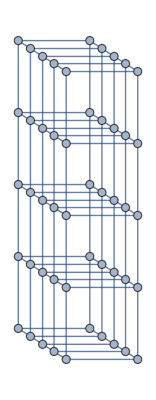
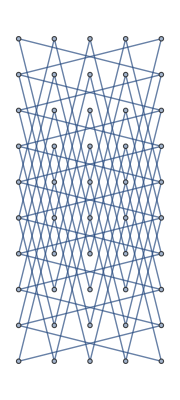
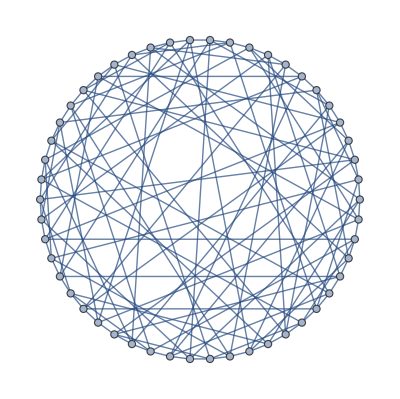
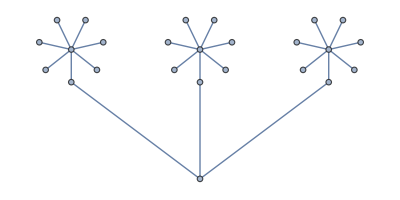
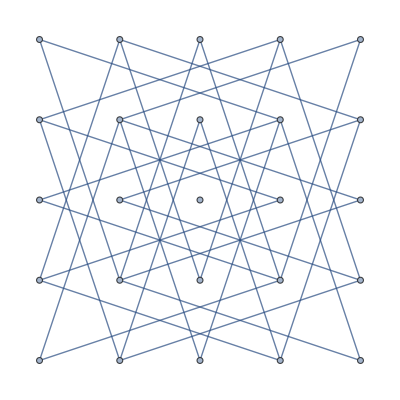
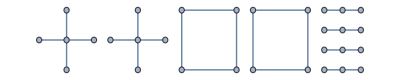
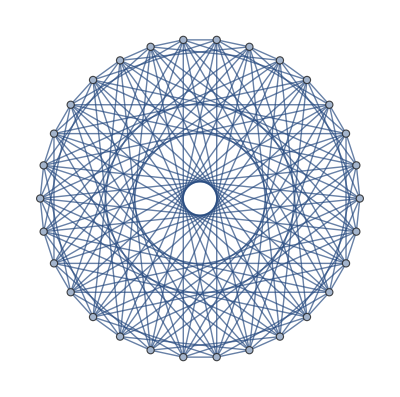
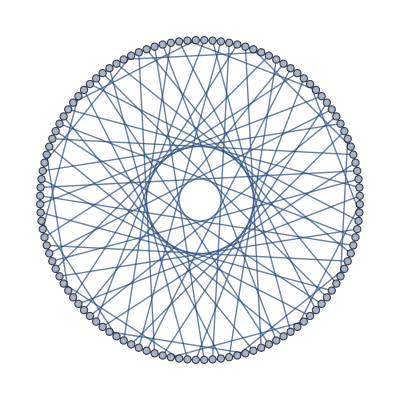
```mathematica
L={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

### Exercise Subsection

The number of triangles in the graph (a cycle of length 3) is equal to (1/6)*(The sum of the cubes of the Eigenvalues of the adjacency matrix of G).  Sort the following list (see SortBy) according to the number of triangles in each graph.

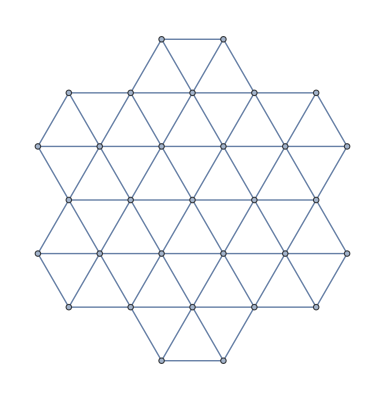
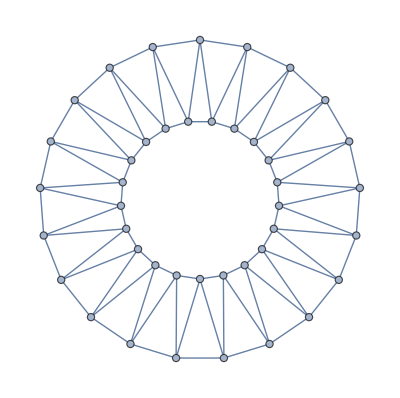
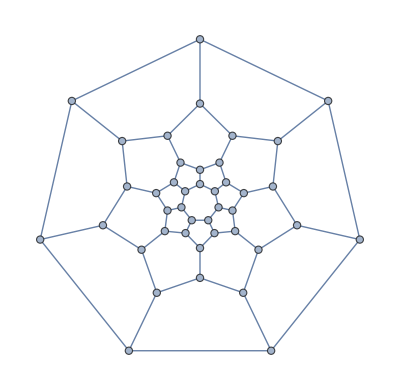
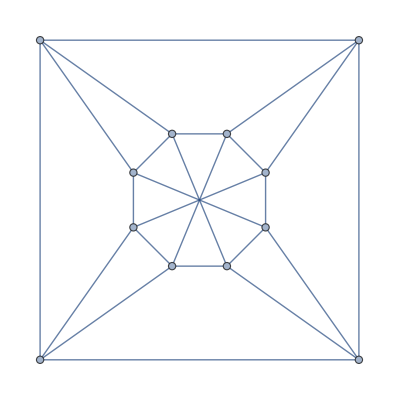
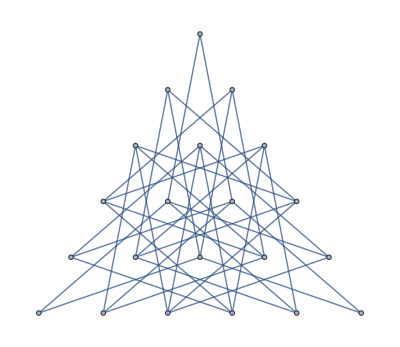
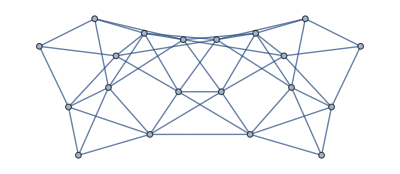
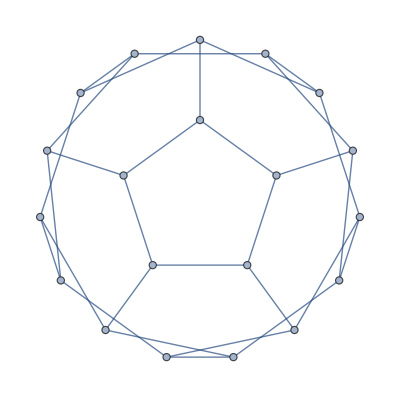
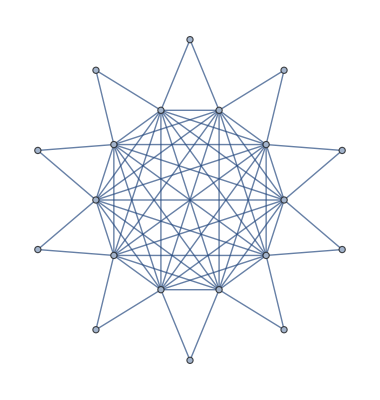
```mathematica
L={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics- ,-Graphics-};
```

### Exercise Subsection

A tree is a connected graph without a cycle.  A spanning tree in a graph G is a tree found by deleting edges in G.  The function FindSpanningTree@G finds a spanning tree in a graph, for example:

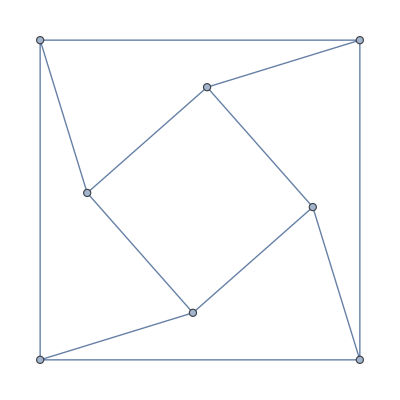
```mathematica
G=-Graphics-;
HighlightGraph[G,FindSpanningTree[G]]
```

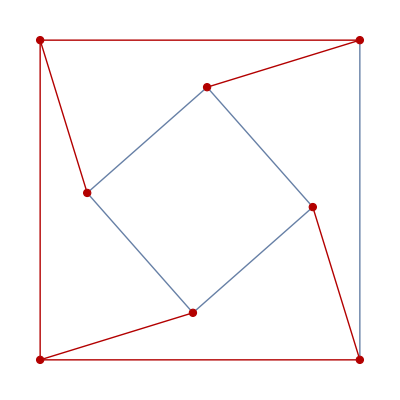

The Matrix Tree Theorem (see https://en.wikipedia.org/wiki/Kirchhoff%27s_theorem ) says that the number of spanning trees for a connected graph with n vertices is equal to (1/n)(the product of the nonzero eigenvalues of KirchhoffMatrix@G).  Sort the graphs in the following list by their number of spanning trees:

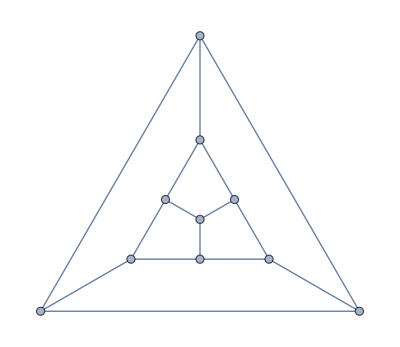
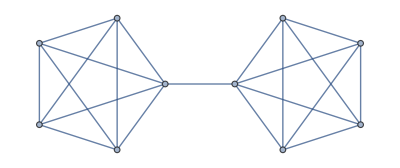
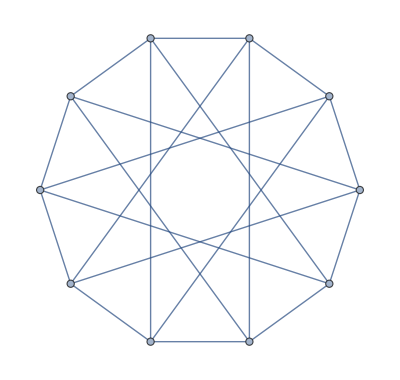
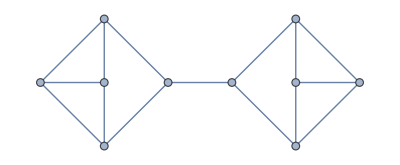
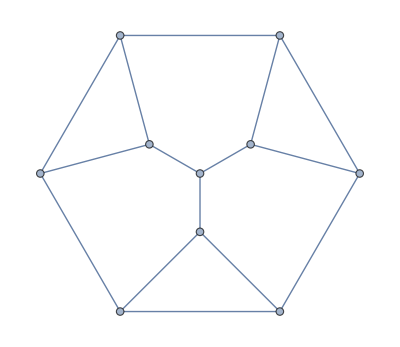
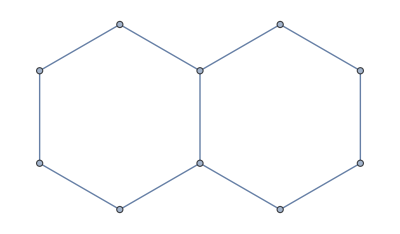
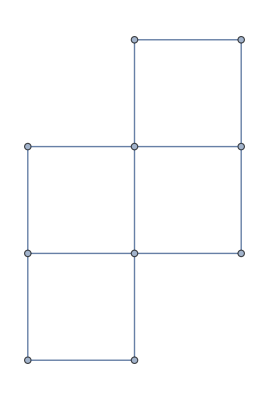
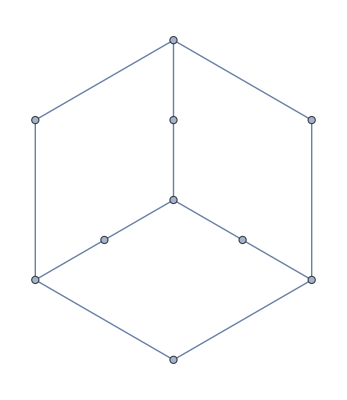
```mathematica
L={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```